## Monte Carlo Playground

```mathematica
unitSalesByQuarterInMillions = {
{"Q1", 25},
{"Q2", 50},
{"Q3", 100},
{"Q4", 75}
};
annualUnitSales = Total[unitSalesByQuarterInMillions][[2]];
normalizedUnitSales = unitSalesByQuarterInMillions[[All,2]]/= annualUnitSales;
normalizedUnitSales = N[normalizedUnitSales]
```

{0.1,0.2,0.4,0.3}

```mathematica
position=RandomInteger[{1,4}];
accumulator = ConstantArray[0,4];
iterations = 10000;
wrapUpper[n_]:=If[n<=4,n, 1]
wrapLower[n_]:=If[n>=1,n, 4]
wrap[n_]:=wrapUpper[wrapLower[n]]
explorations = RandomInteger[{0,1},iterations]*2-1;
accumulate[z_]:=(
newPosition=wrap[position+z];
ratio=normalizedUnitSales[[newPosition]]/(normalizedUnitSales[[newPosition]]+normalizedUnitSales[[position]]);
position = If[RandomReal[]<ratio,newPosition,position];
accumulator[[position]]+=1;
)
Map[accumulate,explorations];
expected=normalizedUnitSales*iterations;
```

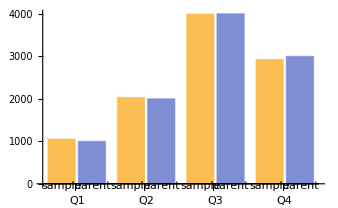

```mathematica
BarChart[Transpose[{accumulator,expected}],ChartLabels->{unitSalesByQuarterInMillions[[All,1]],{"sample","parent"}}]
```